```mathematica
Clear["Global`*"]
```

## Modules

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/future_brr_new/";*)
```

```mathematica
(*dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_Tiingo/";*)
```

```mathematica
dataDirectory=NotebookDirectory[] <> "../processed_data/BBT_future_BITW70/";
```

```mathematica
methods={"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"};
```

```mathematica
Clear[α,β,μ,δ]
```

```mathematica
δs[α_,β_]:=N[(α^2-β^2)^(3/2)/α^2 ]
μs[α_,β_]:=N[-(δs[α,β] β)/(√(α^2-β^2))]
```

General distribution functions

```mathematica
FNIG[x_,α_,β_,μ_,δ_]:=Module[{v},
v=Catch[CDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x], _SystemException];
If[NumberQ[v],v,0]
]
fNIG[x_,α_,β_,μ_,δ_]:=PDF[HyperbolicDistribution[-1/2, α, β, δ, μ],x]
InvFNIG[p_,α_,β_,μ_,δ_]:=InverseCDF[HyperbolicDistribution[-1/2, α, β, δ, μ],p]
```

Standardised distribution functions (mean 0, standard deviation 1)

```mathematica
NIGInv[p_,α_,β_]:=N[InverseCDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], p]]
NIGCDF[x_?NumericQ,α_?NumericQ,β_?NumericQ]:=CDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]],x]
NIGPDF[x_,α_,β_]:=PDF[HyperbolicDistribution[-1/2, α, β, δs[α,β], μs[α,β]], x]
```

```mathematica
FNIGi[α_?NumericQ,β_?NumericQ,μ_?NumericQ,δ_?NumericQ]:=Module[{a,b,r,x},
a=InvFNIG[0.0000001,α,β,μ,δ];
b= InvFNIG[0.9999999,α,β,μ,δ];
r=Range[a,b,(b-a)/70];
Interpolation[Table[{x,FNIG[x,α,β,μ,δ]}, {x, r}]]
]
```

```mathematica
F2NIG2[x_?NumericQ,y_?NumericQ,α_?NumericQ,β_?NumericQ,μ1_?NumericQ,δ_?NumericQ,δ1_?NumericQ, F1_]:=
Module[{a,b},
(*F1=FNIGi[α,β,μ1,δ1];*)
NIntegrate[F1[x-z]F1[y-z]  fNIG[z,α,β,0,δ], {z,-∞,∞},PrecisionGoal->2]
]
```

```mathematica
CNIG2[u_?NumericQ,v_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=F2NIG2[NIGInv[u,α,β],NIGInv[v,α,β],α,β,N[μs[α,β]],δ,N[δs[α,β]]-δ,F1]
```

```mathematica
QDemp[q_,x1_,x2_]:=Module[{q1, q2, sel},
q1=Sort[x1]⟦Round[q Length[x1]]⟧;
q2=Sort[x2]⟦Round[q Length[x2]]⟧;
If[0<q≤0.5,
sel=Select[{x1,x2}ᵀ, #1⟦1⟧<=q1&&#1⟦2⟧<=q2&];
Length[sel]/(q Length[x1]),
sel=Select[{x1,x2}ᵀ, #1⟦1⟧>q1&&#1⟦2⟧>q2&];
Length[sel]/((1-q)Length[x1])
]
]
```

```mathematica
QD[q_?NumericQ,α_?NumericQ,β_?NumericQ,δ_?NumericQ, F1_]:=Module[{cn,k},
If[0<q≤0.5, CNIG2[q,q,α,β,δ,F1]/q,(1-2q+ CNIG2[q,q,α,β,δ,F1])/(1-q)]
]
```

Empirical DF (values lie strictly in [0,1])

```mathematica
Clear[hatF]
```

```mathematica
hatF[x_,s_]:=Module[{n,k},
n=Length[s];
If[Length[x]==0,
N[1/(n+1) Length[Select[s, #1≤x&]]],
Table[N[1/(n+1) Length[Select[s, #1≤x⟦k⟧&]]], {k,1,Length[x]}]
]
]
```

```mathematica
(* empirical df applied to sample itself *)
hatF[s_]:=Module[{n,k,x},
n=Length[s];
x=Sort[s];
Table[N[1/(n+1)Position[x,s⟦k⟧]⟦1,1⟧],{k,1,Length[s]}]
]
```

```mathematica
Clear[obj]
```

```mathematica
(* note that const needs to be defined outside *)
obj[α_?NumericQ,β_?NumericQ, target_]:=Module[{F1,f,q0,q,δ,β0},
If[β≤-α||β≥α,Return[1,Module]];
δ=const δs[α,β];
F1=FNIGi[α,β,μs[α,β], δs[α,β]-δ];
f= Table[QD[q0, α,β,δ,F1]/.q0->q, {q,{0.05,0.1, 0.9, 0.95}}];
Sqrt[Total[(target-f)^2]]
]
```

```mathematica
calibrate[data_]:=calibrate[data, 0.5,0]
```

```mathematica
calibrate[data_,α0_,β0_]:=Module[{q,target,f,α,β,δ,q0,F1,t,sol},
target=Table[QDemp[q,data⟦;;,1⟧,data⟦;;,2⟧],{q,{0.05,0.1,0.9,0.95}}];
(*Print[target];*)
t=Timing[sol=NMinimize[{obj[α,β,target],α>0 &&Abs[β]<α}, {{α,Max[α0-0.5,0],α0+0.5},{β,β0-0.1,β0+0.1}}, Method->"NelderMead", PrecisionGoal->1, AccuracyGoal->1(*,EvaluationMonitor:>Print["α = " <> ToString[α] <> ", β = " <>  ToString[β] <> ", val = " <> ToString[obj[α,β,target]]]*)]];
(*Print[t];*)
(*Print["[calibrate] α, β: " <> ToString[{α,β}]];*)
{α/.sol⟦2⟧,β/.sol⟦2⟧,sol⟦1⟧,t⟦1⟧}
]
```

```mathematica
InSampeCalibrateAndSimulate[data_]:=InSampeCalibrateAndSimulate[data,0.5,0]
```

```mathematica
InSampeCalibrateAndSimulate[data_, α0_,β0_]:=Module[{hatqd, target, sol,α,β,δ,μ, μ1,μ2, δ1,δ2,γ,μIG, μ1IG, μ2IG,λ, λ1, λ2, Y, W, W1, W2, Z, Z1, Z2, X1, X2, usim, vsim},
hatqd=Table[QDemp[q,data⟦1;;All,1⟧,data⟦1;;All,2⟧],{q,{0.05,0.1,0.9,0.95}}];
target=Flatten[Join[{SpearmanRho[data⟦1;;All,1⟧,data⟦1;;All,2⟧]},hatqd]];
const=Sin[1/6 target⟦1⟧ π] 2;
sol=calibrate[data,α0,β0];
α=sol⟦1⟧; 
β=sol⟦2⟧;
δ=const δs[α,β];
μ=0;
μ1=μ2=μs[α,β];
δ1=δ2=δs[α,β]-δ;
γ=√(α^2-β^2);
μIG=δ/γ;
μ1IG=δ1/γ;
μ2IG=δ2/γ;
λ=δ^2;
λ1=δ1^2;
λ2=δ2^2;
Y=RandomVariate[NormalDistribution[],{3,n}];
W = RandomVariate[InverseGaussianDistribution[μIG,λ], n];
W1 = RandomVariate[InverseGaussianDistribution[μ1IG,λ1], n];
W2 = RandomVariate[InverseGaussianDistribution[μ2IG, λ2], n];
Z=μ+β W+√W Y⟦3⟧;
Z1=μ1+β W1+√W1 Y⟦1⟧;
Z2=μ2+β W2+√W2 Y⟦2⟧;
X1 = Z + Z1;
X2 = Z + Z2;
usim = hatF[X1];
vsim = hatF[X2];
{α,β,δ, usim, vsim}
]
```

```mathematica
Clear[r]
r[h_?NumericQ]:=rs -h rf;
```

```mathematica
Clear[ES]
ES[h_?NumericQ,q_?NumericQ]:=Module[{s,k},
s=Sort[r[h]];
k=Ceiling[Length[s] (1-q)];
-Mean[s[[;;k]]]
]
```

```mathematica
Clear[f, SpectralRisk];
f[s_, p_?NumericQ, k_?NumericQ]:=
k/(1-Exp[-k]) Exp[-k(1-p)] Quantile[s,p];
SpectralRisk[h_?NumericQ, k_?NumericQ]:=Module[{s},
s=r[h];
NIntegrate[f[s,p,k], {p,0,1}, AccuracyGoal->4]
]
```

```mathematica
RiskMeasures[rbtc_, rbrr_,usim_, vsim_]:=Module[{dbtc, dbrr,h, hvar,hVaR99, hVaR95, hES99, hES95,hSR10, hSR20,sol,solutions},
dbrr=EmpiricalDistribution[rbrr];
dbtc=EmpiricalDistribution[rbtc];
rs=InverseCDF[dbrr, usim];
rf=InverseCDF[dbtc, vsim];
solutions={};
Print["Variance"];
(*sol=NMinimize[Variance[r[h]], h];*)
hvar=Correlation[rf,rs] StandardDeviation[rs]/StandardDeviation[rf];
Print["VaR 99"];
sol=NMinimize[-Quantile[r[h],0.01], h];
AppendTo[solutions,sol];
hVaR99 = h/.sol[[2]];
Print["VaR 95"];
sol=NMinimize[-Quantile[r[h],0.05], h];
AppendTo[solutions,sol];
hVaR95 = h/.sol[[2]];
Print["ES 99"];
sol = NMinimize[{Abs[ES[h,0.99]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES99 = h/.sol[[2]];
Print["ES 95"];
sol=NMinimize[{Abs[ES[h,0.95]], -1≤h≤2},h];
AppendTo[solutions,sol];
hES95 = h/.sol[[2]];
Print["Spectral 10"];
sol=NMinimize[SpectralRisk[h,10],h];
AppendTo[solutions,sol];
hSR10 = h/.sol[[2]];
(*Print["Spectral 20"];*)
(*sol=NMinimize[SpectralRisk[h,20],h];
AppendTo[solutions,sol];
hSR20 = h/.sol[[2]];*)
{hvar, hVaR99, hVaR95, hES99, hES95, hSR10, solutions}
]
```

```mathematica
HedgeEffectiveness[h_] := Module[{v},
v={};
AppendTo[v,1-Variance[r[h⟦1⟧]]/Variance[rs]];
AppendTo[v,1-Quantile[r[h⟦2⟧],0.01]/Quantile[rs, 0.01]];
AppendTo[v, 1-Quantile[r[h⟦3⟧],0.05]/Quantile[rs, 0.05]];
AppendTo[v,1-ES[h⟦4⟧,0.99]/ES[0,0.99]];
AppendTo[v,1-ES[h⟦5⟧,0.95]/ES[0,0.95]];
AppendTo[v,1-SpectralRisk[h⟦6⟧,10]/SpectralRisk[0,10]];
v
]
```

## Run modules

```mathematica
SeedRandom[123456];
n=50000;
```

```mathematica
heInsample={};
heOutsample={};
```

```mathematica
(*kk=0;
data = 
Import[NotebookDirectory[] <> "../processed_data/coingecko_future_v3/train/" <> ToString[kk] <> ".csv"];*)
```

```mathematica
kk=0;
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
```

CAREFUL: spot and future are the other way round in BRR data set

```mathematica
(*data[[1;;10]]*)
```

( | Date | bitcoin price | Close | log return bitcoin | log return future
5 | 2021-01-27 | 31038.2 | 31905. | -0.0310281 | -0.0204754
6 | 2021-01-26 | 32016.3 | 32565. | -0.0128355 | -0.0492799
7 | 2021-01-25 | 32429.9 | 34210. | -0.0323413 | -0.00160643
8 | 2021-01-22 | 33495.9 | 34265. | 0.0683149 | 0.0507328
9 | 2021-01-21 | 31284. | 32570. | -0.110154 | -0.0966491
10 | 2021-01-20 | 34927.1 | 35875. | -0.041842 | -0.0462983
11 | 2021-01-19 | 36419.5 | 37575. | 0.0068495 | 0.0280682
12 | 2021-01-15 | 36170.9 | 36535. | -0.0686241 | -0.103525
13 | 2021-01-14 | 38740.2 | 40520. | 0.0316585 | 0.0819984)

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | BITW70 Price | % Change | log return future | log return BITW70
5 | 2021-05-20 20:00:00+00:00 | 40350. | BTCM1 Curncy | 66494.6 | 3.56% | 0.0212907 | 0.0349856
6 | 2021-05-19 20:00:00+00:00 | 39500. | BTCM1 Curncy | 64208.5 | -27.64% | -0.0904653 | -0.323453
7 | 2021-05-18 20:00:00+00:00 | 43240. | BTCM1 Curncy | 88729.2 | 3.52% | -0.0196938 | 0.0345513
8 | 2021-05-17 20:00:00+00:00 | 44100. | BTCM1 Curncy | 85715.8 | -0.35% | -0.131645 | -0.109017
9 | 2021-05-14 20:00:00+00:00 | 50305. | BTCM1 Curncy | 95588.7 | 8.73% | 0.03685 | 0.0836779
10 | 2021-05-13 20:00:00+00:00 | 48485. | BTCM1 Curncy | 87915.6 | -10.53% | -0.119603 | -0.111227
11 | 2021-05-12 20:00:00+00:00 | 54645. | BTCM1 Curncy | 98258.7 | -1.26% | -0.042369 | -0.0126896
12 | 2021-05-11 20:00:00+00:00 | 57010. | BTCM1 Curncy | 99513.6 | 6.52% | 0.018947 | 0.0631607
13 | 2021-05-10 20:00:00+00:00 | 55940. | BTCM1 Curncy | 93422.6 | -6.54% | -0.0359909 | -0.110025)

```mathematica
Dimensions[data]
```

{301,8}

```mathematica
StringSplit[data[[2,2]]][[1]]
```

2021-05-20

```mathematica
data[[1,8]]
```

log return BITW70

```mathematica
data[[1,7]]
```

log return future

```mathematica
α0=0.5; β0=0;
```

```mathematica
For[kk=39, kk≥0, kk--,
Print[kk];
SeedRandom[123456];
data =   
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,7⟧;
rbrr=data⟦2;;All,8⟧;
{α,β,δ,usim,vsim}=InSampeCalibrateAndSimulate[data⟦2;;All,7;;8⟧];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv", {DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}],α,β,δ}];Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv", {usim, vsim}ᵀ];
α0=α; β0=β;
]
```

39

38

37

36

35

34

33

32

31

30

29

28

27

26

25

24

23

22

21

20

19

18

17

16

15

14

13

12

11

10

9

8

7

6

5

4

3

2

1

0

```mathematica
{α0,β0}
```

{0.460214,-0.0405146}

```mathematica
dataDirectory
```

/Users/nat/Documents/GitHub/optimal_hedging_ratio_copula/_mathematica/../processed_data/BBT_future_Tiingo_xrp/

```mathematica
For[kk=0, kk≤80, kk++,
Print[kk];
data = 
Import[dataDirectory <> "train/" <> ToString[kk] <> ".csv"];
data2= Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
rbtc=data⟦2;;All,7⟧;
rbrr=data⟦2;;All,8⟧;
{dates2,α,β,δ}=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_parameters.csv" ];utmp = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_simulation.csv"];usim=utmp⟦1;;All,1⟧;
vsim=utmp⟦1;;All,2⟧;
Print["Risk Measures..."];
h=RiskMeasures[rbtc, rbrr, usim, vsim];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv", Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]}, h]];
he=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]]; (* in-sample *)
AppendTo[heInsample, he];
(* out-of-sample *)
rs=data2⟦2;;All,8⟧;
rf=data2⟦2;;All,7⟧;
he2=Join[{DateString[dates⟦1⟧,{"Year","-","Month","-","Day"}]},HedgeEffectiveness[h⟦1;;6⟧]];
AppendTo[heOutsample, he2];
]
```

0

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.975582383567401}. NIntegrate obtained 0.0916138 and 0.000127199 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

1

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.975582383567401}. NIntegrate obtained 0.0911655 and 0.000111256 for the integral and error estimates.

2

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in p near {p} = {0.975582383567401}. NIntegrate obtained 0.0913062 and 0.00011976 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

3

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

4

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

5

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

6

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

7

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

8

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

9

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

10

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

11

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

12

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

13

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

14

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

15

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

16

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

17

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

18

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

19

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

20

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

21

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

22

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

23

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

24

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

25

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

26

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

27

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

28

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

29

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

30

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

31

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

32

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

33

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

34

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

35

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

36

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

37

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

38

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

39

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

40

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

41

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

42

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

43

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

44

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

45

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

46

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

47

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

48

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

49

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

50

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

51

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

52

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

53

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

54

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

55

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

56

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

57

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

58

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

59

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

60

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

61

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

62

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

63

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

64

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

65

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

66

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

67

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

68

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

69

Risk Measures...

Variance

VaR 99

VaR 95

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

ES 99

ES 95

Spectral 10

70

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

71

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

72

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

73

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

74

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

NMinimize::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

75

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

76

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

77

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

78

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

79

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

80

Risk Measures...

Variance

VaR 99

VaR 95

ES 99

ES 95

Spectral 10

## Hedge effectiveness

```mathematica
t1=TableForm[heInsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-20 | 0.467047 | 0.351228 | 0.35003 | 0.210066 | 0.243634 | 0.278364
 | 2021-05-13 | 0.495808 | 0.35833 | 0.338644 | 0.293631 | 0.298401 | 0.282476
 | 2021-05-06 | 0.476139 | 0.355155 | 0.347586 | 0.286438 | 0.285924 | 0.264896
 | 2021-04-29 | 0.494263 | 0.363308 | 0.344337 | 0.295912 | 0.293944 | 0.284529
 | 2021-04-22 | 0.487286 | 0.365929 | 0.336097 | 0.287485 | 0.284152 | 0.28048
 | 2021-04-15 | 0.47837 | 0.362311 | 0.28268 | 0.294895 | 0.284068 | 0.272249
 | 2021-04-08 | 0.477654 | 0.362311 | 0.284741 | 0.295371 | 0.284943 | 0.264248
 | 2021-04-01 | 0.477811 | 0.353393 | 0.253753 | 0.279133 | 0.27685 | 0.289914
 | 2021-03-25 | 0.464828 | 0.354842 | 0.286422 | 0.278737 | 0.274954 | 0.262113
 | 2021-03-18 | 0.458206 | 0.348893 | 0.279758 | 0.276032 | 0.268735 | 0.26183
 | 2021-03-11 | 0.465851 | 0.359193 | 0.274214 | 0.283081 | 0.272494 | 0.248391
 | 2021-03-04 | 0.462215 | 0.350733 | 0.280801 | 0.279165 | 0.271224 | 0.246522
 | 2021-02-25 | 0.454678 | 0.35713 | 0.274943 | 0.280432 | 0.26408 | 0.244437
 | 2021-02-18 | 0.439832 | 0.350093 | 0.271787 | 0.291082 | 0.242532 | 0.257488
 | 2021-02-10 | 0.463873 | 0.37208 | 0.303644 | 0.311599 | 0.262911 | 0.257819
 | 2021-02-03 | 0.483367 | 0.376495 | 0.310091 | 0.311178 | 0.273342 | 0.291411
 | 2021-01-27 | 0.501752 | 0.395876 | 0.328286 | 0.331121 | 0.287799 | 0.292959
 | 2021-01-20 | 0.481661 | 0.383537 | 0.318857 | 0.324901 | 0.282663 | 0.276532
 | 2021-01-12 | 0.487821 | 0.385521 | 0.292901 | 0.308479 | 0.273046 | 0.301111
 | 2021-01-05 | 0.489876 | 0.386374 | 0.313596 | 0.317179 | 0.280268 | 0.299615
 | 2020-12-28 | 0.483658 | 0.374231 | 0.31769 | 0.308456 | 0.270643 | 0.296841
 | 2020-12-18 | 0.480458 | 0.391781 | 0.32171 | 0.322169 | 0.287622 | 0.263962
 | 2020-12-11 | 0.482343 | 0.393621 | 0.328095 | 0.324879 | 0.292418 | 0.261032
 | 2020-12-04 | 0.471464 | 0.391899 | 0.331551 | 0.316648 | 0.286585 | 0.25232
 | 2020-11-27 | 0.494228 | 0.465462 | 0.346998 | 0.317927 | 0.320781 | 0.265127
 | 2020-11-19 | 0.477492 | 0.48608 | 0.33353 | 0.343974 | 0.30336 | 0.231419
 | 2020-11-12 | 0.492169 | 0.496438 | 0.360783 | 0.356134 | 0.318135 | 0.248696
 | 2020-11-05 | 0.494983 | 0.491686 | 0.354475 | 0.35656 | 0.315401 | 0.254036
 | 2020-10-29 | 0.527163 | 0.510115 | 0.398665 | 0.374954 | 0.341531 | 0.280973
 | 2020-10-22 | 0.525254 | 0.508679 | 0.398332 | 0.36373 | 0.340501 | 0.279551
 | 2020-10-15 | 0.529682 | 0.516555 | 0.407754 | 0.381426 | 0.346886 | 0.262863
 | 2020-10-08 | 0.522727 | 0.50248 | 0.397728 | 0.377034 | 0.335529 | 0.265169
 | 2020-10-01 | 0.510544 | 0.499663 | 0.385307 | 0.370172 | 0.32752 | 0.256273
 | 2020-09-24 | 0.500388 | 0.497761 | 0.38989 | 0.366734 | 0.322284 | 0.247433
 | 2020-09-17 | 0.486217 | 0.467864 | 0.337282 | 0.334912 | 0.31983 | 0.224444
 | 2020-09-10 | 0.498152 | 0.473611 | 0.339639 | 0.351944 | 0.324334 | 0.226246
 | 2020-09-02 | 0.518358 | 0.491161 | 0.392077 | 0.359694 | 0.349914 | 0.253205
 | 2020-08-26 | 0.472713 | 0.44808 | 0.341618 | 0.316425 | 0.301516 | 0.255284
 | 2020-08-19 | 0.461071 | 0.437311 | 0.328377 | 0.310188 | 0.291667 | 0.250345
 | 2020-08-12 | 0.473424 | 0.445187 | 0.352785 | 0.33039 | 0.305902 | 0.252513
 | 2020-08-05 | 0.463984 | 0.427054 | 0.349968 | 0.321081 | 0.307516 | 0.22897
 | 2020-07-29 | 0.47954 | 0.437744 | 0.353641 | 0.331591 | 0.315617 | 0.241
 | 2020-07-22 | 0.518618 | 0.47393 | 0.40769 | 0.355001 | 0.354846 | 0.250372
 | 2020-07-15 | 0.514982 | 0.449151 | 0.367516 | 0.34368 | 0.326671 | 0.294081
 | 2020-07-08 | 0.503282 | 0.436204 | 0.351013 | 0.325679 | 0.314203 | 0.294765
 | 2020-06-30 | 0.512205 | 0.434452 | 0.361398 | 0.334334 | 0.327524 | 0.288979
 | 2020-06-23 | 0.496066 | 0.42719 | 0.341711 | 0.326456 | 0.315323 | 0.280117
 | 2020-06-16 | 0.494989 | 0.422411 | 0.352042 | 0.320336 | 0.31161 | 0.277996
 | 2020-06-09 | 0.497386 | 0.419293 | 0.336786 | 0.319777 | 0.305719 | 0.298357
 | 2020-06-02 | 0.494337 | 0.422009 | 0.333414 | 0.31421 | 0.302476 | 0.296409
 | 2020-05-26 | 0.505772 | 0.426326 | 0.349004 | 0.328649 | 0.312889 | 0.298416
 | 2020-05-18 | 0.503471 | 0.42168 | 0.351086 | 0.321214 | 0.311495 | 0.298452
 | 2020-05-11 | 0.494249 | 0.421441 | 0.338568 | 0.322443 | 0.305253 | 0.291651
 | 2020-05-04 | 0.497959 | 0.427426 | 0.33894 | 0.32389 | 0.307102 | 0.293262
 | 2020-04-27 | 0.510759 | 0.422035 | 0.378411 | 0.324175 | 0.318217 | 0.301936
 | 2020-04-20 | 0.509607 | 0.425739 | 0.371737 | 0.327516 | 0.316996 | 0.299366
 | 2020-04-13 | 0.504879 | 0.430217 | 0.349518 | 0.325463 | 0.310334 | 0.300855
 | 2020-04-03 | 0.497857 | 0.425335 | 0.349253 | 0.322103 | 0.308949 | 0.298796
 | 2020-03-27 | 0.490133 | 0.422419 | 0.344609 | 0.319067 | 0.304628 | 0.288492
 | 2020-03-20 | 0.489353 | 0.416971 | 0.361474 | 0.317151 | 0.310966 | 0.276624
 | 2020-03-13 | 0.471853 | 0.405259 | 0.324659 | 0.308379 | 0.309061 | 0.27707
 | 2020-03-06 | 0.474847 | 0.331003 | 0.348871 | 0.211484 | 0.279273 | 0.293343
 | 2020-02-28 | 0.475483 | 0.327258 | 0.345857 | 0.207212 | 0.291508 | 0.2708
 | 2020-02-21 | 0.495039 | 0.32288 | 0.332708 | 0.206673 | 0.277516 | 0.324452
 | 2020-02-13 | 0.503092 | 0.324422 | 0.355836 | 0.212117 | 0.2924 | 0.326789
 | 2020-02-06 | 0.515466 | 0.32747 | 0.343377 | 0.211003 | 0.288612 | 0.34286
 | 2020-01-30 | 0.541418 | 0.291879 | 0.39214 | 0.197589 | 0.322402 | 0.351181
 | 2020-01-23 | 0.549018 | 0.430509 | 0.439546 | 0.262685 | 0.354922 | 0.332154
 | 2020-01-15 | 0.546502 | 0.417681 | 0.428493 | 0.264015 | 0.343019 | 0.343795
 | 2020-01-08 | 0.535107 | 0.418063 | 0.418644 | 0.25728 | 0.338269 | 0.33388
 | 2019-12-31 | 0.533385 | 0.413697 | 0.42069 | 0.256272 | 0.338324 | 0.330092
 | 2019-12-23 | 0.523115 | 0.401953 | 0.417112 | 0.251977 | 0.330591 | 0.321308
 | 2019-12-16 | 0.529942 | 0.406671 | 0.429179 | 0.257635 | 0.335653 | 0.32281
 | 2019-12-09 | 0.532112 | 0.40689 | 0.434335 | 0.259165 | 0.339752 | 0.324779
 | 2019-12-02 | 0.53455 | 0.408393 | 0.436823 | 0.260014 | 0.341202 | 0.326257
 | 2019-11-22 | 0.533496 | 0.410441 | 0.430994 | 0.254835 | 0.337025 | 0.332522
 | 2019-11-15 | 0.52359 | 0.403883 | 0.43354 | 0.251085 | 0.333368 | 0.321863
 | 2019-11-08 | 0.539397 | 0.399749 | 0.455419 | 0.24703 | 0.34312 | 0.331867
 | 2019-11-01 | 0.548392 | 0.40877 | 0.442503 | 0.252434 | 0.342116 | 0.348881
 | 2019-10-25 | 0.539594 | 0.380344 | 0.464325 | 0.219987 | 0.350113 | 0.325269
 | 2019-10-18 | 0.522125 | 0.34043 | 0.42291 | 0.183711 | 0.327069 | 0.327377

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.csv", Prepend[heInsample,{"Variance", "VaR 99%", "VaR 95%", "ES 99%", "ES 95%", "Spectral 10"}]];
```

```mathematica
TableForm[heOutsample, TableHeadings->{{},Join[{"Date"}, methods]}]
```

| Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
 | 2021-05-20 | 0.605842 | 0.358798 | 0.472482 | 0.540621 | 0.470526 | 0.243884
 | 2021-05-13 | 0.431287 | 0.208105 | 0.261596 | 0.207487 | 0.249207 | 0.31589
 | 2021-05-06 | 0.646943 | 0.250823 | 0.264678 | 0.246586 | 0.273591 | 0.252416
 | 2021-04-29 | 0.846126 | 0.728641 | 0.751786 | 0.724035 | 0.840903 | 0.43514
 | 2021-04-22 | 0.611366 | 0.290022 | 0.297632 | 0.283949 | 0.319441 | 0.363405
 | 2021-04-15 | 0.775711 | 0.789767 | 0.806265 | 0.77972 | 0.84372 | -1.42766
 | 2021-04-08 | -0.195272 | -4.49015 | -4.66953 | -4.38839 | -5.03152 | 0.21825
 | 2021-04-01 | 0.624717 | 0.447393 | 0.470261 | 0.509001 | 0.52533 | 0.316793
 | 2021-03-25 | 0.893533 | -0.351858 | -0.371054 | -0.344684 | -0.382418 | 0.558642
 | 2021-03-18 | 0.85766 | 0.745749 | 0.789543 | 0.736544 | 0.810054 | 0.425008
 | 2021-03-11 | 0.363806 | 0.572782 | 0.587077 | 0.560551 | 0.589163 | 0.0137679
 | 2021-03-04 | 0.232779 | -2.15669 | -2.27992 | -2.12832 | -2.31078 | 0.50275
 | 2021-02-25 | 0.785244 | 0.408944 | 0.427672 | 0.398816 | 0.423928 | 0.655732
 | 2021-02-18 | 0.744694 | 0.533566 | 0.526935 | 0.520588 | 0.518406 | 0.330537
 | 2021-02-10 | -0.00231579 | -0.19187 | -0.188038 | -0.184237 | -0.184078 | 0.114277
 | 2021-02-03 | 0.616197 | 0.400454 | 0.291318 | 0.205208 | 0.275442 | 0.447008
 | 2021-01-27 | -0.123262 | 2.23143 | 2.14278 | 2.13438 | 2.17377 | 0.204604
 | 2021-01-20 | 0.889092 | 0.884015 | 0.874573 | 0.871435 | 0.882565 | 0.340054
 | 2021-01-12 | 0.0110443 | -0.546492 | -0.515143 | -0.50002 | -0.840136 | 0.114708
 | 2021-01-05 | 0.458137 | 0.2969 | 0.304452 | 0.295997 | 0.300563 | 0.158908
 | 2020-12-28 | 0.510729 | -0.054233 | -0.0677647 | -0.0539248 | -0.0592084 | 0.415435
 | 2020-12-18 | 0.680636 | 0.0224661 | 0.021539 | 0.0223257 | 0.0237198 | 0.77516
 | 2020-12-11 | -2.56758 | 62.1062 | 62.0247 | 61.7027 | 66.8471 | 0.456801
 | 2020-12-04 | 0.145105 | 0.285488 | 0.284807 | 0.277913 | 0.299496 | 0.0162983
 | 2020-11-27 | 0.614372 | 0.347372 | 0.0095361 | 0.342927 | 0.0245432 | 0.621689
 | 2020-11-19 | 0.523591 | 0.525624 | 0.52352 | 0.512574 | 0.584799 | -0.0838253
 | 2020-11-12 | 0.232165 | 0.0651868 | 0.0659044 | 0.0630382 | 0.0745991 | 0.0790276
 | 2020-11-05 | -0.262937 | -0.568278 | -0.546622 | -0.552862 | -0.63699 | 0.210065
 | 2020-10-29 | 0.909443 | -0.0846833 | -0.100566 | -0.0822794 | -0.0972412 | 1.19316
 | 2020-10-22 | 0.757205 | 0.273317 | 0.192771 | 0.276555 | 0.208709 | 3.21274
 | 2020-10-15 | 0.469609 | -0.278 | -0.329023 | -0.266847 | -0.311217 | 0.805525
 | 2020-10-08 | 0.593948 | 0.364944 | 0.376523 | 0.35557 | 0.37127 | 0.439236
 | 2020-10-01 | 0.501334 | 0.197065 | 0.20344 | 0.189733 | 0.218147 | 0.50881
 | 2020-09-24 | 0.475055 | 0.255393 | 0.307698 | 0.244912 | 0.282982 | 0.222023
 | 2020-09-17 | 0.586964 | 0.274189 | 0.267406 | 0.273218 | 0.309842 | 0.47407
 | 2020-09-10 | -0.223788 | -0.159501 | -0.171151 | -0.156474 | -0.176787 | 0.150994
 | 2020-09-02 | 0.533874 | 0.355232 | 0.362802 | 0.34374 | 0.357025 | 0.199945
 | 2020-08-26 | 0.537273 | 0.23414 | 0.230983 | 0.233197 | 0.235828 | 0.252662
 | 2020-08-19 | 0.433541 | 0.439565 | 0.463566 | 0.433932 | 0.428527 | 0.112082
 | 2020-08-12 | 0.409714 | 0.224486 | 0.218923 | 0.221916 | 0.218834 | 0.303679
 | 2020-08-05 | 0.469841 | 0.595107 | 0.64119 | 0.584933 | 0.585134 | 0.107609
 | 2020-07-29 | -1.88349 | -2.01966 | -1.81417 | -2.00387 | -2.0243 | -0.0370643
 | 2020-07-22 | -2.39889 | -1.82027 | -1.59458 | -1.79787 | -1.75781 | 0.179455
 | 2020-07-15 | -0.396189 | 2.9891 | 2.89615 | 2.91157 | 2.88396 | 0.0897781
 | 2020-07-08 | 0.497869 | 1.2058 | 1.18807 | 1.19662 | 1.18822 | 0.00651458
 | 2020-06-30 | 0.602965 | 1.26471 | 1.25337 | 1.27303 | 1.26034 | 0.210756
 | 2020-06-23 | 0.355265 | 0.293602 | 0.297363 | 0.290006 | 0.294004 | -1.48751
 | 2020-06-16 | 0.854742 | 0.770799 | 0.816227 | 0.756129 | 0.770114 | 0.386995
 | 2020-06-09 | 0.650584 | 0.603937 | 0.630952 | 0.593207 | 0.594847 | 0.184835
 | 2020-06-02 | -5.17296 | 2.16887 | 2.1978 | 2.14089 | 2.14169 | -0.0901282
 | 2020-05-26 | -0.695249 | -4.57133 | -4.68284 | -4.45969 | -4.50756 | 0.529065
 | 2020-05-18 | 0.51714 | 1.21309 | 1.28147 | 1.1854 | 1.19373 | 0.0279177
 | 2020-05-11 | 0.079267 | -1.27326 | -1.37471 | -1.21069 | -1.21645 | 0.177426
 | 2020-05-04 | 0.82884 | 0.657396 | 0.634453 | 0.664402 | 0.661552 | 0.118852
 | 2020-04-27 | 0.378932 | -0.722703 | -1.1744 | -0.62855 | -0.797719 | 0.589034
 | 2020-04-20 | -0.726542 | 2.264 | 2.55272 | 2.18328 | 2.26133 | 0.509613
 | 2020-04-13 | 0.773544 | 0.60621 | 0.64184 | 0.595747 | 0.604178 | 0.306658
 | 2020-04-03 | 0.84291 | 0.763156 | 0.761812 | 0.763683 | 0.762985 | 0.4367
 | 2020-03-27 | 0.841187 | 0.654639 | 0.690042 | 0.640759 | 0.661202 | 0.589425
 | 2020-03-20 | 0.582141 | 0.534578 | 0.359442 | 0.528662 | 0.532361 | 0.457539
 | 2020-03-13 | 0.822163 | 0.546393 | 0.550628 | 0.545382 | 0.54924 | 0.435879
 | 2020-03-06 | 0.754616 | 0.469779 | 0.663431 | 0.413013 | 0.555955 | 0.199182
 | 2020-02-28 | 0.687845 | 0.495459 | 0.68464 | 0.395354 | 0.562207 | 0.307701
 | 2020-02-21 | 0.472643 | 0.395543 | 0.489914 | 0.328157 | 0.411159 | 0.0537387
 | 2020-02-13 | 0.605131 | 0.272352 | 0.34613 | 0.252755 | 0.307626 | 0.296153
 | 2020-02-06 | 0.352408 | 0.566883 | 0.78701 | 0.52856 | 0.660179 | 0.113353
 | 2020-01-30 | -0.426097 | 4.21808 | 18.2246 | 2.99306 | 11.5624 | -0.0141099
 | 2020-01-23 | -0.708765 | 2.82476 | 3.91045 | 2.1836 | 3.60562 | 0.605004
 | 2020-01-15 | 0.729049 | 0.461499 | 0.706576 | 0.424804 | 0.59995 | 0.318379
 | 2020-01-08 | 0.674801 | 0.937997 | 0.100107 | 0.892502 | 0.631297 | 0.351688
 | 2019-12-31 | 0.0353903 | -1.1204 | -2.21176 | -1.02853 | -1.74408 | 0.694136
 | 2019-12-23 | 0.0959008 | 0.0970033 | 0.0621845 | 0.0992284 | 0.0778977 | 0.0236493
 | 2019-12-16 | 0.618307 | 0.173094 | 0.0235103 | 0.18385 | 0.0855578 | 0.679748
 | 2019-12-09 | 0.348633 | 0.0971012 | 0.158581 | 0.0932898 | 0.132813 | -0.181505
 | 2019-12-02 | 0.718953 | 0.818265 | 0.899299 | 0.6728 | 0.905909 | 0.212035
 | 2019-11-22 | 0.799939 | 0.649105 | 0.707535 | 0.616014 | 0.848138 | 0.307959
 | 2019-11-15 | 0.766793 | 0.507465 | 0.736109 | 0.445984 | 0.619782 | 1.20829
 | 2019-11-08 | 0.368634 | 0.813583 | 1.03191 | 0.78742 | 0.926375 | -0.370891
 | 2019-11-01 | 0.77047 | 0.740644 | 0.887731 | 0.619303 | 0.780464 | 0.273167
 | 2019-10-25 | 0.924796 | 0.818306 | -1.34581 | 0.815463 | -0.321887 | 0.787724
 | 2019-10-18 | 0.74257 | 0.695304 | 0.191157 | 0.688676 | 0.350013 | 0.622264

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.csv", Prepend[heOutsample,methods]];
```

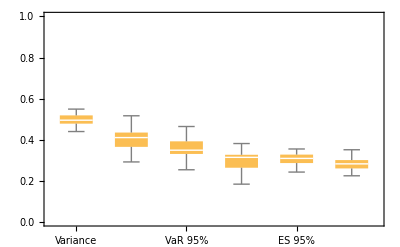

```mathematica
BoxWhiskerChart[Transpose[heInsample⟦1;;All,2;;All⟧],ChartLabels->methods,PlotRange->{0,1}]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample_box.png", %];
```

```mathematica
dates=Table[DateList[{heInsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heInsample⟦1;;All,1⟧]}];
```

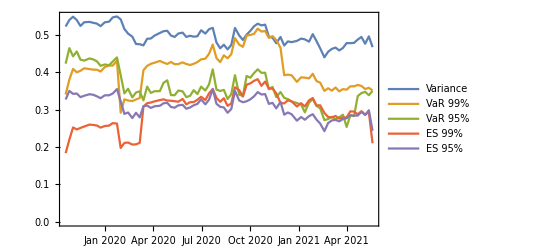

```mathematica
DateListPlot[Table[{dates,heInsample[[;;,k]]}ᵀ, {k,2,Dimensions[heInsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Insample.png", %];
```

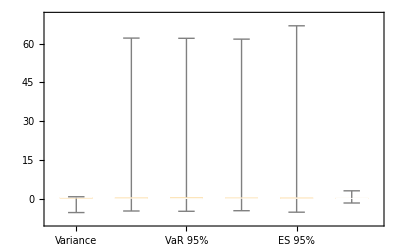

```mathematica
BoxWhiskerChart[heOutsample[[;;,2;;]]ᵀ, ChartLabels->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample_box.png", %];
```

```mathematica
dates=Table[DateList[{heOutsample⟦k,1⟧,{"Year","Month","Day"}}],{k,1,Length[heOutsample⟦1;;All,1⟧]}];
```

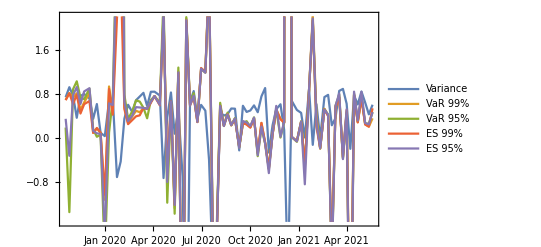

```mathematica
DateListPlot[Table[{dates,heOutsample[[;;,k]]}ᵀ, {k,2,Dimensions[heOutsample][[2]]-1}],PlotLegends->methods]
```

```mathematica
Export[NotebookDirectory[] <> "data/HedgeEffectiveness_Outsample.png", %];
```

## P&L

```mathematica
data[[1,8]]
```

log return BITW70

```mathematica
data[[1,7]]
```

log return future

```mathematica
data[[2,2]]
```

2019-10-18 20:00:00+00:00

### In-sample P&L

```mathematica
For[kk=0, kk≤80, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];
btc=Reverse[data⟦2;;All,8⟧];
brr=Reverse[data⟦2;;All,7⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc = Exp[btc]-1;
rbtc = Log[1+PLbtc];
PrependTo[PLbtc, "future"];
AppendTo[PL,PLbtc];
PrependTo[rbtc, "future"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv",PLrᵀ]
]
```

```mathematica
data[[1;;10]]
```

( | Date | PX_LAST | contract_name | BITW70 Price | % Change | log return future | log return BITW70
405 | 2019-10-18 20:00:00+00:00 | 7990. | BTCX19 Curncy | 4686.83 | -2.27% | -0.0142904 | -0.0229841
406 | 2019-10-17 20:00:00+00:00 | 8105. | BTCX19 Curncy | 4795.8 | 3.24% | 0.0142904 | 0.0318738
407 | 2019-10-16 20:00:00+00:00 | 7990. | BTCX19 Curncy | 4645.35 | -5.44% | -0.0295953 | -0.0559733
408 | 2019-10-15 20:00:00+00:00 | 8230. | BTCX19 Curncy | 4912.78 | -1.87% | -0.0222298 | -0.0188532
409 | 2019-10-14 20:00:00+00:00 | 8415. | BTCX19 Curncy | 5006.28 | -0.07% | 0. | 0.0187595
410 | 2019-10-11 20:00:00+00:00 | 8415. | BTCX19 Curncy | 4913.24 | -2.53% | -0.0275435 | -0.025655
411 | 2019-10-10 20:00:00+00:00 | 8650. | BTCX19 Curncy | 5040.92 | -1.53% | -0.00403808 | -0.0153705
412 | 2019-10-09 20:00:00+00:00 | 8685. | BTCX19 Curncy | 5119. | 1.61% | 0.0544191 | 0.0159678
413 | 2019-10-08 20:00:00+00:00 | 8225. | BTCX19 Curncy | 5037.91 | 2.06% | -0.00787167 | 0.020357)

```mathematica
hvec
```

{{2019-10-18},{0.818442},{0.653014},{0.946107},{0.646789},{0.854473},{0.71048},{{0.1330094407491555, {h$192630143 -> 0.6530141361613091}},{0.06604626160276625, {h$192630143 -> 0.9461071062307672}},{0.16947308410765413, {h$192630143 -> 0.6467893764176165}},{0.10790891887598952, {h$192630143 -> 0.854472726054301}},{0.048021091573674936, {h$192630143 -> 0.7104800291997405}}}}

### Out-of-sample P&L

```mathematica
For[kk=0, kk≤80, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,8⟧];
brr=Reverse[data⟦2;;All,7⟧];
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj,1⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh, methods⟦jj-1⟧];
AppendTo[PL, PLh];
PrependTo[rh, methods⟦jj-1⟧];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv",PLrᵀ]
]
```

### Sandbox P&L in-sample

```mathematica
For[kk=0, kk≤80, kk++,
data = 
Import[dataDirectory <>"train/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,8⟧];
brr=Reverse[data⟦2;;All,7⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_insample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv",PLrᵀ]
]
```

### Sandbox P&L out-of-sample

```mathematica
For[kk=0, kk<=80, kk++,
data = 
Import[dataDirectory <>"test/" <> ToString[kk] <> ".csv"];
dates=Table[DateList[{StringSplit[data⟦k,2⟧][[1]],{"Year","Month","Day"}}],{k,2,Length[data⟦1;;All,2⟧]}];btc=Reverse[data⟦2;;All,8⟧];
brr=Reverse[data⟦2;;All,7⟧];
hvec = Join[{""},Range[0.5, 1.5, 0.1]];
PL={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]};
PLr={Join[{"Date"},Table[ DateString[dates⟦k⟧,{"Year","-","Month","-","Day"}], {k,1,Length[dates]}]]}; (* P&L as log returns *)
PLbrr=Exp[brr]-1;
rbrr=Log[1+PLbrr];
PrependTo[PLbrr, "unhedged"];
AppendTo[PL, PLbrr];
PrependTo[rbrr, "unhedged"];
AppendTo[PLr, rbrr];
PLbtc=Exp[btc]-1;
rbtc=Log[1+PLbtc];
PrependTo[PLbtc, "unhedged"];
AppendTo[PL, PLbtc];
PrependTo[rbtc, "unhedged"];
AppendTo[PLr, rbtc];
For[jj=2, jj≤Length[hvec⟦2;;-2⟧]+1,jj++,
h=hvec⟦jj⟧;
V0=1-h;
Vh=Exp[brr] - h Exp[btc];
PLh=Vh-V0;
rh=Log[(1+PLh)];
PrependTo[PLh,ToString[hvec[[jj]]]];
AppendTo[PL, PLh];
PrependTo[rh,ToString[hvec[[jj]]]];
AppendTo[PLr, rh];
];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PL_sandbox_outsample.csv",PLᵀ];
Export[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv",PLrᵀ]
]
```

## Plots

In-sample
This doesn’t make much sense as the samples are overlapping, so it’s not clear which h to associate with which time period in-sample.

```mathematica
d={};
For[kk=0, kk≤80, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

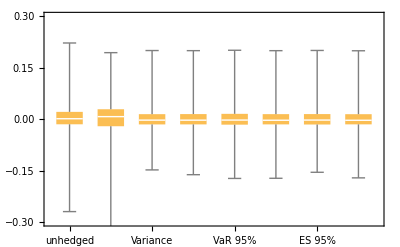

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

The overlap is clearly visible below.

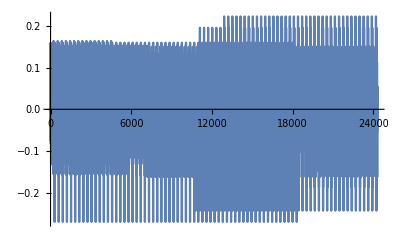

```mathematica
ListPlot[d[[2;;,2]], Joined->True,PlotRange->Full]
```

Out-of-sample

```mathematica
d={};
For[kk=0, kk≤80, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

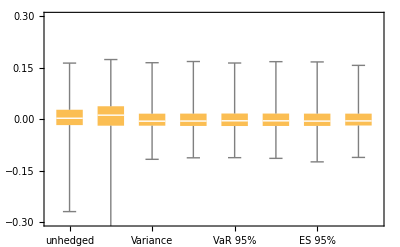

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

```mathematica
dates=Table[DateList[{d⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[d⟦2;;All,1⟧]}];
```

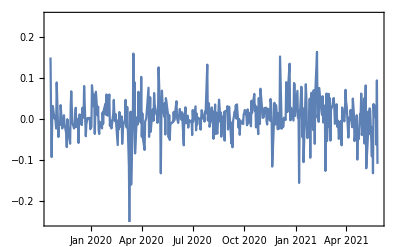
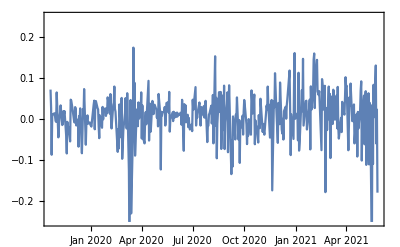

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25}], {m,2,3}]
```

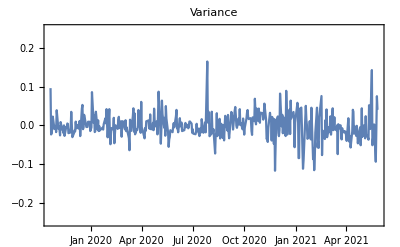
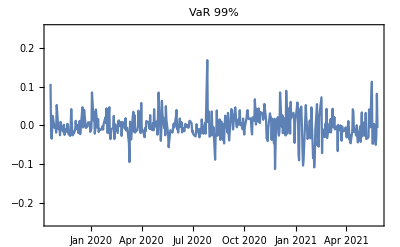
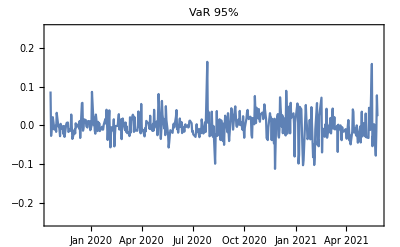
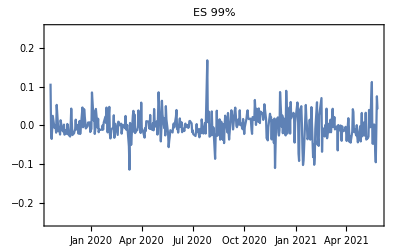
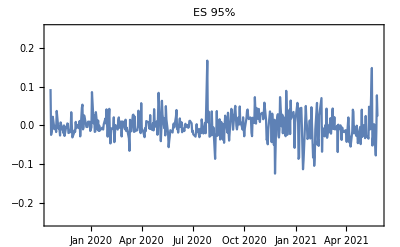
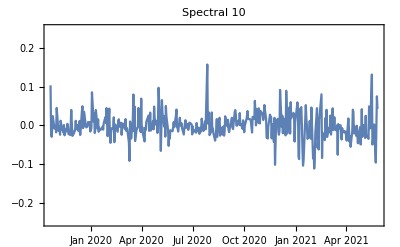

```mathematica
Table[DateListPlot[{dates,d[[2;;,m]]}ᵀ,PlotRange->{-0.25,0.25},PlotLabel->methods[[m-3]]], {m,4,9}]
```

Sandbox in-sample

```mathematica
d={};
For[kk=0, kk≤80, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_insample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

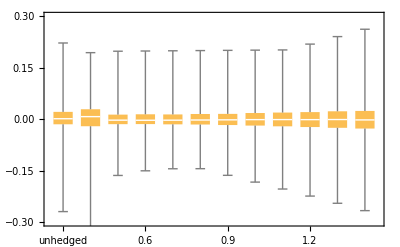

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

Sandbox out-of-sample

```mathematica
d={};
For[kk=0, kk≤80, kk++,
d1=Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_PLr_sandbox_outsample.csv"];
If[kk==0,
d=Join[d,d1],
d=Join[d,d1[[2;;]]]
];
]
```

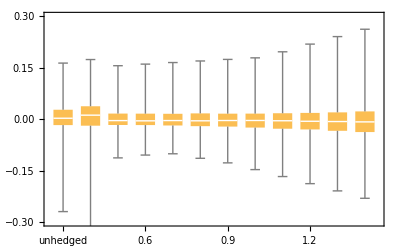

```mathematica
BoxWhiskerChart[d[[2;;,2;;]]ᵀ, ChartLabels->d[[1,2;;]],PlotRange->{Automatic, {-0.3, 0.3}}]
```

h time series

```mathematica
h={Join[{"Date"},methods]};
For[kk=0, kk≤80, kk++,
hvec = Import[NotebookDirectory[] <> "data/" <> ToString[kk] <> "_h.csv"];
h=Join[h,{hvec[[;;-2,1]]}];
]
```

```mathematica
dates=Table[DateList[{h⟦k+1,1⟧,{"Year","Month","Day"}}],{k,1,Length[h⟦2;;All,1⟧]}];
```

```mathematica
h
```

(Date | Variance | VaR 99% | VaR 95% | ES 99% | ES 95% | Spectral 10
2021-05-20 | 0.88018 | 0.58982 | 0.776704 | 0.888714 | 0.773488 | 0.894369
2021-05-13 | 0.868314 | 0.744064 | 0.935319 | 0.741857 | 0.891022 | 0.820448
2021-05-06 | 0.850559 | 0.741738 | 0.784558 | 0.728644 | 0.812102 | 0.819724
2021-04-29 | 0.874928 | 0.750035 | 0.773859 | 0.745294 | 0.865592 | 0.858941
2021-04-22 | 0.867066 | 0.752762 | 0.772514 | 0.737001 | 0.829122 | 0.842487
2021-04-15 | 0.865248 | 0.748622 | 0.776789 | 0.731468 | 0.840739 | 0.847228
2021-04-08 | 0.863239 | 0.748622 | 0.778528 | 0.731655 | 0.838881 | 0.843317
2021-04-01 | 0.856962 | 0.75439 | 0.79295 | 0.858272 | 0.885807 | 0.848167
2021-03-25 | 0.842269 | 0.740072 | 0.780446 | 0.724983 | 0.804348 | 0.841806
2021-03-18 | 0.837297 | 0.734043 | 0.777149 | 0.724983 | 0.797339 | 0.833683
2021-03-11 | 0.835985 | 0.746794 | 0.770983 | 0.726096 | 0.774513 | 0.853607
2021-03-04 | 0.831406 | 0.735368 | 0.777386 | 0.725695 | 0.787906 | 0.828164
2021-02-25 | 0.82377 | 0.742691 | 0.776704 | 0.724297 | 0.769904 | 0.845891
2021-02-18 | 0.810013 | 0.752762 | 0.743408 | 0.734453 | 0.731374 | 0.844057
2021-02-10 | 0.824331 | 0.777317 | 0.761795 | 0.746396 | 0.745752 | 0.89251
2021-02-03 | 0.844717 | 0.782485 | 0.764458 | 0.750234 | 0.761836 | 0.853163
2021-01-27 | 0.840965 | 0.803892 | 0.771956 | 0.76893 | 0.783119 | 0.819882
2021-01-20 | 0.829359 | 0.797122 | 0.763691 | 0.752583 | 0.791989 | 0.817819
2021-01-12 | 0.838345 | 0.792328 | 0.786594 | 0.783827 | 0.846038 | 0.793511
2021-01-05 | 0.847762 | 0.778662 | 0.956722 | 0.757357 | 0.865032 | 0.817086
2020-12-28 | 0.819936 | 0.759132 | 0.948543 | 0.754817 | 0.828776 | 0.740346
2020-12-18 | 0.81879 | 0.778214 | 0.746098 | 0.773351 | 0.821642 | 0.769361
2020-12-11 | 0.82727 | 0.781285 | 0.78026 | 0.776209 | 0.840925 | 0.772149
2020-12-04 | 0.816455 | 0.785149 | 0.783275 | 0.764315 | 0.823674 | 0.749347
2020-11-27 | 0.84826 | 0.813347 | 0.959889 | 0.802938 | 0.954213 | 0.73788
2020-11-19 | 0.822427 | 0.789283 | 0.786124 | 0.769687 | 0.87814 | 0.705992
2020-11-12 | 0.833662 | 0.802388 | 0.811221 | 0.775941 | 0.918245 | 0.724844
2020-11-05 | 0.82219 | 0.796376 | 0.766027 | 0.774772 | 0.892667 | 0.719942
2020-10-29 | 0.853166 | 0.819694 | 0.973426 | 0.796425 | 0.941248 | 0.76046
2020-10-22 | 0.851222 | 0.818663 | 0.97416 | 0.812413 | 0.943391 | 0.769039
2020-10-15 | 0.852568 | 0.827842 | 0.97978 | 0.794629 | 0.926757 | 0.753108
2020-10-08 | 0.833431 | 0.810034 | 0.977576 | 0.779401 | 0.901567 | 0.708576
2020-10-01 | 0.818052 | 0.806469 | 0.832556 | 0.776462 | 0.892744 | 0.685205
2020-09-24 | 0.805966 | 0.805717 | 0.970729 | 0.772651 | 0.892757 | 0.678133
2020-09-17 | 0.793266 | 0.766235 | 0.747279 | 0.763522 | 0.86587 | 0.690785
2020-09-10 | 0.797085 | 0.775578 | 0.832228 | 0.760859 | 0.859631 | 0.624187
2020-09-02 | 0.739822 | 0.802945 | 0.820057 | 0.776969 | 0.806998 | 0.561518
2020-08-26 | 0.675317 | 0.745863 | 0.735806 | 0.74286 | 0.751242 | 0.511233
2020-08-19 | 0.656311 | 0.745006 | 0.785685 | 0.735459 | 0.726298 | 0.517395
2020-08-12 | 0.662231 | 0.744406 | 0.725958 | 0.735883 | 0.725661 | 0.492804
2020-08-05 | 0.643868 | 0.733342 | 0.790129 | 0.720804 | 0.721053 | 0.453471
2020-07-29 | 0.65425 | 0.738141 | 0.663038 | 0.73237 | 0.739837 | 0.463778
2020-07-22 | 0.689139 | 0.765176 | 0.670302 | 0.75576 | 0.73892 | 0.521226
2020-07-15 | 0.668044 | 0.749887 | 0.734033 | 0.736663 | 0.731953 | 0.518227
2020-07-08 | 0.658767 | 0.73699 | 0.726154 | 0.731375 | 0.726241 | 0.521704
2020-06-30 | 0.671392 | 0.74094 | 0.753965 | 0.726392 | 0.745952 | 0.522566
2020-06-23 | 0.660651 | 0.733914 | 0.750904 | 0.717666 | 0.735725 | 0.518414
2020-06-16 | 0.66224 | 0.726685 | 0.769513 | 0.712855 | 0.726039 | 0.456612
2020-06-09 | 0.657353 | 0.730195 | 0.762857 | 0.717222 | 0.719203 | 0.516487
2020-06-02 | 0.657573 | 0.726386 | 0.734452 | 0.718584 | 0.718807 | 0.522854
2020-05-26 | 0.667196 | 0.732095 | 0.744116 | 0.72006 | 0.725221 | 0.51604
2020-05-18 | 0.665965 | 0.728018 | 0.76906 | 0.711401 | 0.716403 | 0.516145
2020-05-11 | 0.662397 | 0.733812 | 0.764503 | 0.714885 | 0.716625 | 0.515983
2020-05-04 | 0.669282 | 0.730433 | 0.770882 | 0.718081 | 0.723106 | 0.516381
2020-04-27 | 0.685842 | 0.726405 | 0.78913 | 0.713331 | 0.736822 | 0.510791
2020-04-20 | 0.685592 | 0.730431 | 0.786045 | 0.714882 | 0.729917 | 0.506767
2020-04-13 | 0.683442 | 0.732707 | 0.775772 | 0.72006 | 0.730251 | 0.555214
2020-04-03 | 0.683365 | 0.729468 | 0.768544 | 0.714136 | 0.73444 | 0.548495
2020-03-27 | 0.681046 | 0.726692 | 0.765991 | 0.711284 | 0.733976 | 0.548385
2020-03-20 | 0.684659 | 0.723906 | 0.776429 | 0.712013 | 0.726874 | 0.54987
2020-03-13 | 0.672919 | 0.722774 | 0.781511 | 0.708758 | 0.762264 | 0.473178
2020-03-06 | 0.649152 | 0.544103 | 0.779357 | 0.478356 | 0.643912 | 0.554403
2020-02-28 | 0.659419 | 0.558158 | 0.771279 | 0.445385 | 0.633353 | 0.603873
2020-02-21 | 0.672786 | 0.635046 | 0.78656 | 0.526857 | 0.660118 | 0.581344
2020-02-13 | 0.678322 | 0.542196 | 0.780258 | 0.478961 | 0.656015 | 0.584442
2020-02-06 | 0.691644 | 0.565836 | 0.785557 | 0.527584 | 0.65896 | 0.659792
2020-01-30 | 0.714022 | 0.514719 | 0.835896 | 0.486629 | 0.683128 | 0.6604
2020-01-23 | 0.743783 | 0.664159 | 0.807299 | 0.579627 | 0.767111 | 0.632679
2020-01-15 | 0.742155 | 0.590975 | 0.904808 | 0.543985 | 0.768268 | 0.652301
2020-01-08 | 0.735229 | 0.597212 | 0.901572 | 0.568245 | 0.759861 | 0.63293
2019-12-31 | 0.739337 | 0.575398 | 0.899882 | 0.548082 | 0.760831 | 0.639746
2019-12-23 | 0.734205 | 0.568275 | 0.900673 | 0.547033 | 0.750667 | 0.632036
2019-12-16 | 0.742457 | 0.566852 | 0.900449 | 0.542866 | 0.762073 | 0.636242
2019-12-09 | 0.74202 | 0.56204 | 0.917896 | 0.539979 | 0.768749 | 0.638583
2019-12-02 | 0.744577 | 0.656049 | 0.920055 | 0.539422 | 0.770297 | 0.65459
2019-11-22 | 0.747257 | 0.588785 | 0.902026 | 0.558769 | 0.769322 | 0.635251
2019-11-15 | 0.742416 | 0.623638 | 0.904625 | 0.548083 | 0.761667 | 0.633115
2019-11-08 | 0.762924 | 0.640376 | 0.891825 | 0.610245 | 0.770279 | 0.690579
2019-11-01 | 0.77242 | 0.755853 | 0.90596 | 0.63202 | 0.79649 | 0.669244
2019-10-25 | 0.798425 | 0.586768 | 0.901087 | 0.582902 | 0.825639 | 0.704614
2019-10-18 | 0.818442 | 0.653014 | 0.946107 | 0.646789 | 0.854473 | 0.71048)

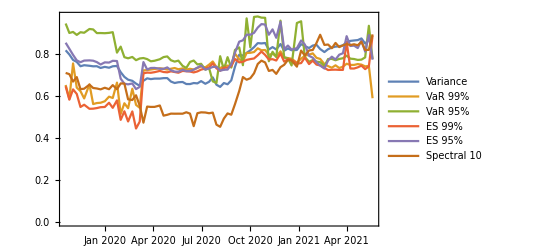

```mathematica
DateListPlot[Table[{dates,h[[2;;,k+1]]}ᵀ, {k,1,Dimensions[h][[2]]-1}],PlotLegends->methods,PlotRange->Full]
```